```mathematica
Manipulate[
K=Interpolation[{
{0,0},
p0,
p1,
p2,p3,
{1,1}}];
G[x_]:=K[x];
{Plot[G[x],{x,0,1},ImageSize->300],
ParametricPlot[{G[a],G[1-a]},{a,0,1}]},
{{p0,{0.2,0.2}},Locator},
{{p1,{0.5,0.5}},Locator},
{{p2,{0.6,0.6}},Locator},
{{p3,{0.7,0.7}},Locator}]
```

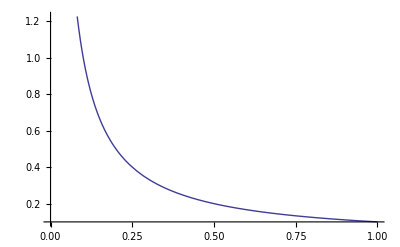

```mathematica
f[x_]:=0.1/x
Plot[f[x],{x,0,1}]
```

{{0.1,0.111111},{0.15,0.117647},{0.2,0.125},{0.25,0.133333},{0.3,0.142857},{0.35,0.153846},{0.4,0.166667},{0.45,0.181818},{0.5,0.2},{0.55,0.222222},{0.6,0.25}}

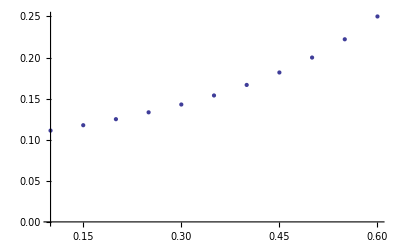

```mathematica
TDC=Table[{x,f[1-x]},{x,0.1,0.6,0.05}]
ListPlot[TDC]
```